# Images

What’s the difference between....

```mathematica
RandomImage[1, {10, 10}]
RandomReal[1, {10, 10}]
```

-Graphics-

{{0.933499,0.427802,0.859816,0.352233,0.916858,0.487509,0.563499,0.849148,0.0531225,0.283338},{0.253244,0.576099,0.204752,0.52492,0.453128,0.0864778,0.770143,0.934852,0.933621,0.994499},{0.517072,0.466193,0.177762,0.604538,0.655931,0.793685,0.841793,0.455954,0.686853,0.272412},{0.177376,0.000339582,0.652923,0.934914,0.502683,0.700734,0.441003,0.0871569,0.23417,0.44531},{0.729943,0.0482799,0.116383,0.119531,0.607527,0.538824,0.372013,0.333993,0.923689,0.398305},{0.15086,0.3587,0.220788,0.400445,0.896915,0.545554,0.410817,0.666539,0.0990634,0.115203},{0.65874,0.459815,0.249491,0.231199,0.72878,0.924344,0.519964,0.0784293,0.882228,0.191137},{0.229608,0.685811,0.454658,0.0310817,0.294794,0.815063,0.200759,0.440915,0.822279,0.796408},{0.861518,0.459672,0.260489,0.439745,0.605301,0.817227,0.91363,0.242554,0.446065,0.658699},{0.860068,0.344206,0.11544,0.822936,0.653601,0.696831,0.870184,0.413621,0.665301,0.273528}}

An image is just array + instructions on how to interpret/display (translation to “quantity of light”)

Can operate using array operations

```mathematica
image = Import["ExampleData/peacock.tif"]
```

-Graphics-

```mathematica
image ^ (1/2.2)
```

-Graphics-

Note that operations can overflow [cause clipping] and be non-invertible (without degradation). Below, info is lost:

```mathematica
ImageSubtract[ImageAdd[image, .5], .5]
```

-Graphics-

```mathematica
im // EdgeDetect // ColorNegate
```

-Graphics-

Can compute image derivatives by convolution with small kernels

```mathematica
PDF[NormalDistribution[0,1],x]
```

(ⅇ^(-x^2/2))/(√(2 π))

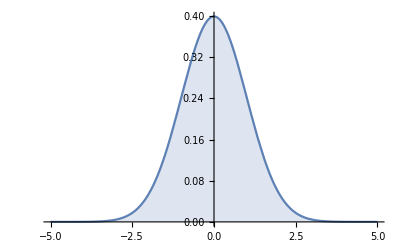

```mathematica
Plot[%, {x, -5, 5}, Filling->Axis]
```

Differentiating produces this left right signs; analogous to a finite difference derivative!

-(ⅇ^(-x^2/2) x)/(√(2 π))

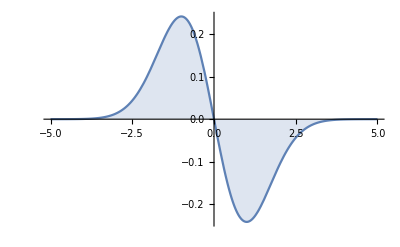

```mathematica
D[PDF[NormalDistribution[0,1],x], x]
Plot[%, {x, -5, 5}, Filling->Axis]
```

Do greater derivs correspond to more accurate finite difference or just greater degree??

(-15 ⅇ^(-x^2/2) x+10 ⅇ^(-x^2/2) x^3-ⅇ^(-x^2/2) x^5)/(√(2 π))

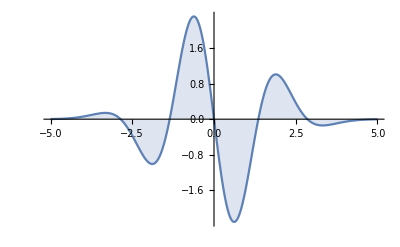

```mathematica
D[PDF[NormalDistribution[0,1],x], {x,5}]
Plot[%, {x, -5, 5}, Filling->Axis]
```

```mathematica
ImageAdjust @ ImageConvolve[image, {{-1, 1}}]
```

-Graphics-

This is showing horizontal variation

```mathematica
ImageAdjust @ ImageConvolve[image, {{1},{-1}}]
```

-Graphics-

and this is showing vertical variation.

Using a bigger kernel size, you’ll consider greater neighbourhoods of pixels, and you can use greater accuracy finite difference expansions.

Use that exponent trick via derivs of the GaussianMatrix to get a very ‘smooth’ derivative

Can use GradientFilter but it will be single channel. So you can channel separate, GradientFilter each 3 color channel, then re-combine

```mathematica
RidgeFilter   (* detects rise and drop of edges. e.g. fingers *)
```

```mathematica
Dilation   (* dilates features in image, using a passed kernel  *)
```

```mathematica
GeodesicDilation   (* dilate an image with a positional mask. E.g. dots on black will select connected components of the mask *)
```